```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]<>"\\MethodsODE\\OutputData\\"];

(* Модуль для создания фазовой плоскости *)
plotfaze[ data_]  := Module[{point, plot},
point = Table[Table[{data[[n]][[i]], data[[n+1]][[i]]}, {i, 1, Length[data[[1]]]}], {n, 1, Length[data]-1, 2}];

plot = ListPlot[point,ImageSize->400,  AxesLabel->{"u1", "u2"}, AxesStyle->Arrowheads[0.03], PlotRange->{{-2, 2}, {-2, 2}}, Frame -> True];

Show[plot]
]
```

```mathematica
data = Import["FZ1", "Table"];
```

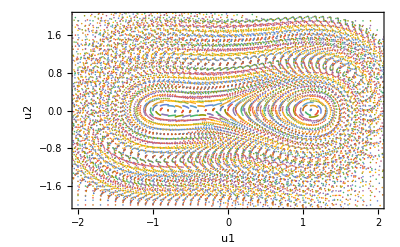

```mathematica
plotfaze[data]
```